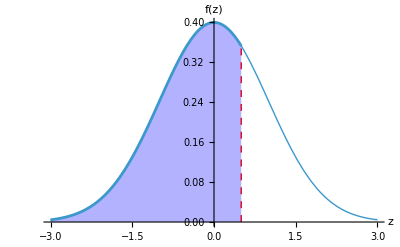

```mathematica
Show[Plot[PDF[NormalDistribution[0,1],x],{x,-3,3},PlotStyle->Thick,AxesLabel->{"z","f(z)"}],Plot[PDF[NormalDistribution[0,1],x],{x,-3,0.5},Filling->Axis,FillingStyle->Directive[Opacity[0.3],Blue]],Graphics[{Red,Dashed,Line[{{0.5,0},{0.5,PDF[NormalDistribution[0,1],0.5]}}],Text[Style["x=0.5",Red,Bold],{0.5,-0.02},{0,1}]}]]
```

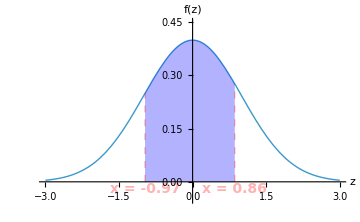

```mathematica
a=-0.97;b=0.86;
f[x_]:=PDF[NormalDistribution[0,1],x];
prob=N[CDF[NormalDistribution[0,1],b]-CDF[NormalDistribution[0,1],a],6];

Show[(*full normal curve*)Plot[f[x],{x,-3,3},PlotStyle->Thick,PlotRange->{{-3,3},{-0.05,0.45}},AxesLabel->{"z","f(z)"}],Graphics[{(*shaded polygon from a to b,down to axis*)Directive[Opacity[0.3],Blue],Polygon[Join[Table[{x,f[x]},{x,a,b,0.01}],{{b,0},{a,0}}]],(*dashed vertical lines at boundaries*){Red,Dashed,Line[{{a,0},{a,f[a]}}]},{Red,Dashed,Line[{{b,0},{b,f[b]}}]},(*labels*)Text[Style["x = -0.97",Red,Bold,14],{a,-0.02},{0,1}],Text[Style["x = 0.86",Red,Bold,14],{b,-0.02},{0,1}]}],ImageSize->Medium]
```